## Figure G.2: Distribution of months between NBER release and journal submission

```mathematica
(*The following command sets the working directory to the project root directory.*)
SetDirectory[ParentDirectory[ParentDirectory[NotebookDirectory[]]]];
Needs["DatabaseLink`"];
JDBCDrivers["SQLite"];
conn = OpenSQLConnection[JDBC["SQLite", Directory[]<>"/0-data/fixed/read.db"]];
font="Avenir Light";
```

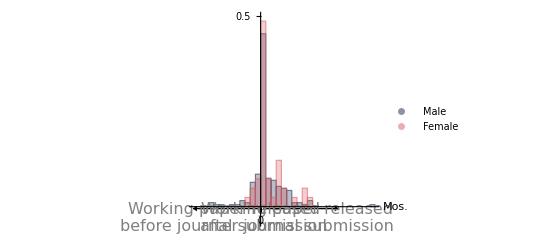

```mathematica
sql="
SELECT 
	ArticleID, NberID, (JULIANDAY(WPDate)-JULIANDAY(Received))/30 AS ReleaseSubmit,
	SUM(CASE WHEN Sex = 'Male' THEN 1 ELSE 0 END) AS Male, COUNT(AuthorID) AS N
	FROM Article
	NATURAL JOIN (SELECT ArticleID, AuthorID, Sex FROM Author NATURAL JOIN AuthorCorr) AS Author
	NATURAL JOIN NBERCorr
	NATURAL JOIN (SELECT NberID, WPDate FROM Nber) AS Nber
	WHERE Received IS NOT NULL AND Journal <> 'RES'
	GROUP BY ArticleID, NberID
";
data= SQLExecute[conn, sql];
male=Select[data,#⟦4⟧==#⟦5⟧&]⟦All,3⟧;
female=Select[data,#⟦4⟧<#⟦5⟧&]⟦All,3⟧;
opacity=Opacity[0.3];
{blue,pink}={RGBColor[26/255,40/255,78/255],RGBColor[216/255,92/255,99/255]};
legend=PointLegend[{blue,pink},{"Male","Female"},
LegendMarkers->Graphics[{EdgeForm[None],Opacity[0.5],Disk[]}],
LegendMarkerSize->20,
LabelStyle->{FontSize->24,FontColor->Gray,FontFamily->font,FontWeight->Plain},
LegendMargins->5,
LegendLayout->"Row"
];
histogram=Histogram[{male,female},{5},"Probability",
ChartStyle->{
Directive[blue,opacity],
Directive[pink,opacity]},
ChartLegends->Placed[legend,{Right,Center}],
AxesStyle->Directive[Thin,Gray,FontFamily->font,FontSize->Medium],
Ticks->{{0},{0.5}},
AxesOrigin->{0,0},
Epilog->{
{Thickness[Tiny],Arrowheads[Small],
Arrow[{{2.5,-0.005},{75,-0.005}}],
Arrow[{{-2.5,-0.005},{-65,-0.005}}]},
Text[Style["Working paper released\nafter journal submission",Gray,FontFamily->font,FontSize->16],{35,-0.03}],
Text[Style["Working paper released\nbefore journal submission",Gray,FontFamily->font,FontSize->16],{-35,-0.03}]
}];
plot=Show[
{histogram},
PlotRange->{{-65,110},{-0.04,0.5}},
AxesLabel->{Style["Mos.",FontSize->16],None},
ImageSize->Full
];
plot
Export["0-images/generated/Figure-G.2.png",plot];
```